```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/xiaonuxiong/Nustore Files/Nutstore/PDF Euclidean Lattice/Hadron_Structure_Lattice/PDF/pion_proton_PDF

```mathematica
StringContainsQ
```

```mathematica
πPntSnkReTags
```

{}

```mathematica
PntSrcPntSnkTag=Select[Import["pion_2pt_no_smr.h5"],StringContainsQ[#,"Re"]&];
```

```mathematica
π2ptPNTPNT=Import["pion_2pt_no_smr.h5",{"Datasets",#}]&/@PntSrcPntSnkTag;
```

```mathematica
ppp=Table[ArcCosh[(#⟦t+1⟧+#⟦t-1⟧)/(2#⟦t⟧)],{t,2,95}]&/@π2ptPNTPNT;
```

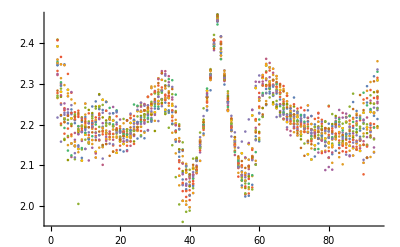

```mathematica
ListPlot[ppp]
```

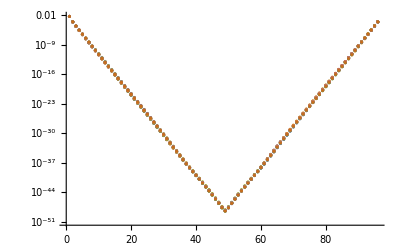

```mathematica
ListLogPlot[π2ptPNTPNT]
```

```mathematica
πPntSnkReTags=Sort[Select[Import["pion_2pt.h5"],StringContainsQ[#,"Re"]&&StringContainsQ[#,__~~"pnt_snk"~~__]&]];
```

```mathematica
πPntSnkImTags=Sort[Select[Import["pion_2pt.h5"],StringContainsQ[#,"Im"]&&StringContainsQ[#,__~~"pnt_snk"~~__]&]];
```

```mathematica
πSnkSmrReTags=Sort[Select[Import["pion_2pt.h5"],StringContainsQ[#,"Re"]&&StringContainsQ[#,__~~"snk_smr"~~__]&]];
```

```mathematica
πSnkSmrImTags=Sort[Select[Import["pion_2pt.h5"],StringContainsQ[#,"Im"]&&StringContainsQ[#,__~~"snk_smr"~~__]&]];
```

```mathematica
πPntSnk=(Import["pion_2pt.h5",{"Datasets",#}]&/@πPntSnkReTags)+I*(Import["pion_2pt.h5",{"Datasets",#}]&/@πPntSnkImTags);
```

```mathematica
πSnkSmr=(Import["pion_2pt.h5",{"Datasets",#}]&/@πSnkSmrReTags)+I*(Import["pion_2pt.h5",{"Datasets",#}]&/@πSnkSmrImTags);
```

```mathematica
πSnkSmr
```

```mathematica
Quit[]
```

```mathematica
LaunchKernels[]
```

{KernelObject(1,local),KernelObject(2,local)}

```mathematica
$ProcessorCount
```

2

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/xiaonuxiong/Nustore Files/Nutstore/PDF Euclidean Lattice/Hadron_Structure_Lattice/PDF/pion_proton_PDF

```mathematica
Import["TwoPtFunc.wdx"]
```

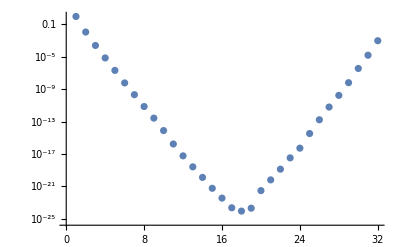

```mathematica
ListLogPlot[Import["TwoPtFunc.wdx"]//Re]
```

```mathematica
tag=Import[".//hdf5//proton_PDF.h5"]
```

{/wilson_k0.1665_b5.32144_4by32_cfg_4000.lime/<P(y,t)|q-bar(x).ga_3.W[x,x+1_stps_in_2].q(x+1_stps_in_2)|P(0,0)>/TwoPnt_tr_prpgtrs/Im,/wilson_k0.1665_b5.32144_4by32_cfg_4000.lime/<P(y,t)|q-bar(x).ga_3.W[x,x+1_stps_in_2].q(x+1_stps_in_2)|P(0,0)>/TwoPnt_tr_prpgtrs/Re,/wilson_k0.1665_b5.32144_4by32_cfg_4000.lime/<P(y,t)|q-bar(x).ga_3.W[x,x+1_stps_in_2].q(x+1_stps_in_2)|P(0,0)>/d_tr_prpgtrs/Im,/wilson_k0.1665_b5.32144_4by32_cfg_4000.lime/<P(y,t)|q-bar(x).ga_3.W[x,x+1_stps_in_2].q(x+1_stps_in_2)|P(0,0)>/d_tr_prpgtrs/Re,/wilson_k0.1665_b5.32144_4by32_cfg_4000.lime/<P(y,t)|q-bar(x).ga_3.W[x,x+1_stps_in_2].q(x+1_stps_in_2)|P(0,0)>/u_tr_prpgtrs/Im,/wilson_k0.1665_b5.32144_4by32_cfg_4000.lime/<P(y,t)|q-bar(x).ga_3.W[x,x+1_stps_in_2].q(x+1_stps_in_2)|P(0,0)>/u_tr_prpgtrs/Re}

```mathematica
p2pnt=Transpose[Table[Fourier[Transpose[I*Import[".//hdf5//proton_PDF.h5",{"Datasets",tag⟦1⟧}]+Import[".//hdf5//proton_PDF.h5",{"Datasets",tag⟦2⟧}],{4,3,2,1}]⟦All,All,All,i⟧,{{1,1,1}},FourierParameters->{1,-1}],{i,1,32}]]⟦1⟧//Re
```

{0.947829,0.0113784,0.000250723,7.22909×10^-6,2.08628×10^-7,5.99382×10^-9,2.11138×10^-10,7.30433×10^-12,2.70559×10^-13,7.88467×10^-15,1.73899×10^-16,5.99575×10^-18,2.6323×10^-19,1.31467×10^-20,5.94723×10^-22,3.65609×10^-23,2.34533×10^-24,9.16287×10^-25,2.09233×10^-24,3.07524×10^-22,6.4904×10^-21,1.35787×10^-19,3.37948×10^-18,5.32723×10^-17,3.39312×10^-15,1.69779×10^-13,6.31495×10^-12,1.743×10^-10,6.38539×10^-9,3.63461×10^-7,0.0000156137,0.000960873}

```mathematica
Import["TwoPtFunc.wdx"]//Re
```

{0.947829,0.0113784,0.000250723,7.22909×10^-6,2.08628×10^-7,5.99382×10^-9,2.11138×10^-10,7.30433×10^-12,2.70559×10^-13,7.88467×10^-15,1.73899×10^-16,5.99575×10^-18,2.6323×10^-19,1.31467×10^-20,5.94723×10^-22,3.65609×10^-23,2.34533×10^-24,9.16287×10^-25,2.09233×10^-24,3.07524×10^-22,6.4904×10^-21,1.35787×10^-19,3.37948×10^-18,5.32723×10^-17,3.39312×10^-15,1.69779×10^-13,6.31495×10^-12,1.743×10^-10,6.38539×10^-9,3.63461×10^-7,0.0000156137,0.000960873}

```mathematica
ListLogPlot[p2pnt]
```

-Graphics-

```mathematica
πtags=Import["pion_2pt.h5"]
```

{/wilson_k0.1665_b5.32144_4by32_cfg_4000.lime/2.200000 10/TwoPnt_pnt_snk/Im,/wilson_k0.1665_b5.32144_4by32_cfg_4000.lime/2.200000 10/TwoPnt_pnt_snk/Re,/wilson_k0.1665_b5.32144_4by32_cfg_4000.lime/2.200000 10/TwoPnt_snk_smr/Im,/wilson_k0.1665_b5.32144_4by32_cfg_4000.lime/2.200000 10/TwoPnt_snk_smr/Re}

```mathematica
ptags=Import["proton_2pt.h5"]
```

{/wilson_k0.1665_b5.32144_4by32_cfg_4000.lime/2.200000 10/TwoPnt_pnt_snk_1/Im,/wilson_k0.1665_b5.32144_4by32_cfg_4000.lime/2.200000 10/TwoPnt_pnt_snk_1/Re,/wilson_k0.1665_b5.32144_4by32_cfg_4000.lime/2.200000 10/TwoPnt_pnt_snk_2/Im,/wilson_k0.1665_b5.32144_4by32_cfg_4000.lime/2.200000 10/TwoPnt_pnt_snk_2/Re,/wilson_k0.1665_b5.32144_4by32_cfg_4000.lime/2.200000 10/TwoPnt_snk_smr_1/Im,/wilson_k0.1665_b5.32144_4by32_cfg_4000.lime/2.200000 10/TwoPnt_snk_smr_1/Re,/wilson_k0.1665_b5.32144_4by32_cfg_4000.lime/2.200000 10/TwoPnt_snk_smr_2/Im,/wilson_k0.1665_b5.32144_4by32_cfg_4000.lime/2.200000 10/TwoPnt_snk_smr_2/Re}

```mathematica
Import["pion_2pt.h5",{"Datasets",πtags⟦2⟧}]
```

```mathematica
(8Import["pion_2pt.h5",{"Datasets",πtags⟦2⟧}])/(First/@Table[Sum[ttt⟦i,j,k,m,n⟧,{j,4},{k,4},{m,4}],{i,1,32},{n,1,2}])
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,0.999998,0.999996,0.99999,0.999991,1.00001,1.00006,1.00025,1.00012,1.00004,1.00001,0.999999,0.999996,0.999997,0.999999,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
p2pnt
```

```mathematica
(8*(Import["proton_2pt.h5",{"Datasets",ptags⟦2⟧}]+Import["proton_2pt.h5",{"Datasets",ptags⟦4⟧}]))/p2pnt
```

{1.,1.,1.,1.,1.,1.,1.,1.,0.999998,1.,1.00002,1.00003,0.99997,0.999412,0.998507,0.997163,0.995578,1.01105,1.08831,1.00541,1.00171,1.00029,1.00002,0.999945,1.,0.999999,1.,1.,1.,1.,1.,1.}

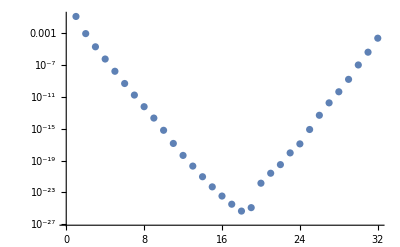

```mathematica
ListLogPlot[2*(Import["proton_2pt.h5",{"Datasets",ptags⟦2⟧}]-Import["proton_2pt.h5",{"Datasets",ptags⟦4⟧}])]
```

```mathematica
p2pnt
```

{0.947829,0.0113784,0.000250723,7.22909×10^-6,2.08628×10^-7,5.99382×10^-9,2.11138×10^-10,7.30433×10^-12,2.70559×10^-13,7.88467×10^-15,1.73899×10^-16,5.99575×10^-18,2.6323×10^-19,1.31467×10^-20,5.94723×10^-22,3.65609×10^-23,2.34533×10^-24,9.16287×10^-25,2.09233×10^-24,3.07524×10^-22,6.4904×10^-21,1.35787×10^-19,3.37948×10^-18,5.32723×10^-17,3.39312×10^-15,1.69779×10^-13,6.31495×10^-12,1.743×10^-10,6.38539×10^-9,3.63461×10^-7,0.0000156137,0.000960873}

```mathematica
Import["TwoPtFunc.wdx"]//Re
```

```mathematica
(2*#⟦2⟧&/@(TomUp+TomDw)⟦2;;-1⟧)/(MmntmPrjctdtrPrpgtrs[TwoPntTrcdPrpgtrs,{0,0,0}]//Re)
```

```mathematica
Import["TwoPtFunc.wdx"]//Re
```

{0.947829,0.0113784,0.000250723,7.22909×10^-6,2.08628×10^-7,5.99382×10^-9,2.11138×10^-10,7.30433×10^-12,2.70559×10^-13,7.88467×10^-15,1.73899×10^-16,5.99575×10^-18,2.6323×10^-19,1.31467×10^-20,5.94723×10^-22,3.65609×10^-23,2.34533×10^-24,9.16287×10^-25,2.09233×10^-24,3.07524×10^-22,6.4904×10^-21,1.35787×10^-19,3.37948×10^-18,5.32723×10^-17,3.39312×10^-15,1.69779×10^-13,6.31495×10^-12,1.743×10^-10,6.38539×10^-9,3.63461×10^-7,0.0000156137,0.000960873}